Cart-pendulum, general case (finite m/M) and set m/(M+m)=A, d=0.

```mathematica
Clear["Global`*"];
ffCartPendulumGeneral[n_,τ_,τ1_,A_]:=Module[{x,xdot,f,θ,θdot,λ1,λ2,λ3,λ4,Δt,bcs,eqns,sv,froot,xff,xdotff,xff0,xdotff0,θff0,θdotff0,uff0,θff,θdotff,uff},Δt=τ/n;
f[{x_,xdot_,θ_,θdot_,λ1_,λ2_,λ3_,λ4_}]:={xdot,1/(1-A Cos[θ]^2)(A θdot^2 Sin[θ]+1/(1-A Cos[θ]^2)(λ4 Cos[θ]-λ2)+A Cos[θ] Sin[θ]),θdot,1/(1-A Cos[θ]^2)(-1/(1-A Cos[θ]^2)(-λ2 Cos[θ]+λ4 Cos[θ]^2)-Sin[θ]-A θdot^2 Cos[θ] Sin[θ]),0,-λ1,2/(A Cos[2 θ]+A-2)^3 (Cos[θ] (4 Sin[θ] (A λ4^2 Cos[2 θ]+4 A λ2^2+(A+2) λ4^2)-(A Cos[2 θ]-3 A+2) (A Cos[2 θ]+A-2) (A θdot^2 λ2-λ4))+A ((A-2) Cos[2 θ]+A) (A Cos[2 θ]+A-2) (λ2-θdot^2 λ4)-4 λ2 λ4 Sin[θ] (3 A Cos[2 θ]+3 A+2)),4/(A Cos[2 θ]+A-2)(A θdot Sin[θ] (λ2-λ4 Cos[θ]))-λ3};
bcs={Subscript[x, 0]==Subscript[xdot, 0]==Subscript[x, n]==Subscript[xdot, n]==Subscript[θ, 0]==Subscript[θdot, 0]==Subscript[θdot, n]==0,Subscript[θ, n]==π};eqns=Flatten[Join[bcs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}==1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}],{i,1,n}]]];sv=Flatten[Table[{{Subscript[x, i],0},{Subscript[xdot, i],0},{Subscript[θ, i],0},{Subscript[θdot, i],0},{Subscript[λ1, i],0},{Subscript[λ2, i],0},{Subscript[λ3, i],0},{Subscript[λ4, i],0}},{i,0,n}],1];froot=FindRoot[eqns,sv];
xff0=ListInterpolation[Table[Subscript[x, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->1];
xdotff0=ListInterpolation[Table[Subscript[xdot, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->1];θff0=ListInterpolation[Table[Subscript[θ, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->1];θdotff0=ListInterpolation[Table[Subscript[θdot, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->1];uff0=ListInterpolation[Table[1/(1-A Cos[Subscript[θ, i]]^2)(Subscript[λ4, i] Cos[Subscript[θ, i]]-Subscript[λ2, i]),{i,0,n}]/.froot,{0,τ},InterpolationOrder->1];

xff[t_]:=Piecewise[{{xff0[t],0≤t≤τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0≤t≤τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0≤t≤τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0≤t≤τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0≤t≤τ}},0];

{xff,xdotff,θff,θdotff,uff}]
```

Test the approximate solution on the open-loop dynamics

```mathematica
TestSwingUpGeneral[τ_,τ1_,uff0_,A_]:=Module[{eq,init,x,xdot,θ,θdot,xs,xdots,θs,θdots,t},
eq={x'[t]==xdot[t],xdot'[t]==1/(1-A Cos[θ[t]]^2)(uff0[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]]),θ'[t]==θdot[t],θdot'[t]==1/(1-A Cos[θ[t]]^2)(-Sin[θ[t]]-Cos[θ[t]] (uff0[t]+A θdot[t]^2 Sin[θ[t]]))};
init={x[0]==xdot[0]==θ[0]==θdot[0]==0};
{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
{xs,θs}]
```

Show that linear feedback can stabilize against “bad” numerics

```mathematica
TestSwingUpGeneralFB[τ_,τ1_,xff0_,xdotff0_,θff0_,θdotff0_,uff0_,A_]:=Module[{eq,init,θ,θdot,θff,θdotff,x,xdot,xff,xdotff,uff,t,κ1,κ2,κ3,κ4,ufb,u,θs,θdots,xs,xdots,us},
κ1=κ2=3;  (* lqr for q=r for balancing pendulum *)
κ3 = -0.1;κ4 = -0.65;
xff[t_]:=Piecewise[{{xff0[t],0≤t≤τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0≤t≤τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0≤t≤τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0≤t≤τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0≤t≤τ}},0];
ufb[t_]:=κ1(θff[t]-θ[t])+κ2 (θdotff[t]-θdot[t])+κ3(xff[t]-x[t])+κ4 (xdotff[t]-xdot[t]);
u[t_]:=uff[t]+ufb[t];
eq={x'[t]==xdot[t],xdot'[t]==1/(1-A Cos[θ[t]]^2)(u[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]]),θ'[t]==θdot[t],θdot'[t]==1/(1-A Cos[θ[t]]^2)(-Sin[θ[t]]-Cos[θ[t]] (u[t]+A θdot[t]^2 Sin[θ[t]]))};
init={x[0]==xdot[0]==θ[0]==θdot[0]==0};
{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
us[t_]:=uff[t]+κ1(θff[t]-θs[t])+κ2 (θdotff[t]-θdots[t])+κ3(xff[t]-xs[t])+κ4 (xdotff[t]-xdots[t]);
{xs,θs,us}]
```

Test example

```mathematica
n=9;τ=4;τ1= τ*1.25 ;
A=0.5; 
{x1a,xdot1a,θ1a,θdot1a,u1a}=ffCartPendulumGeneral[n,τ,τ1,A];  
{x1b,θ1b}=TestSwingUpGeneral[τ,τ1,u1a,A]; 
{x1c,θ1c,u1c}=TestSwingUpGeneralFB[τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A];
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Graphics

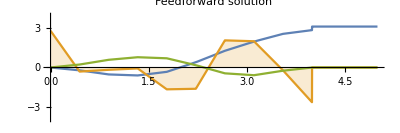
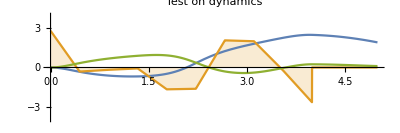
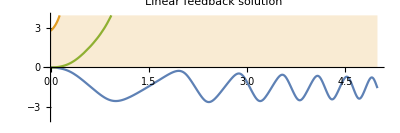
-Graphics- | -Graphics- | -Graphics-

```mathematica
p1a=Plot[{θ1a[t],u1a[t],x1a[t]},{t,0,τ1},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->"Expressions",PlotLabel->"Feedforward solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}];
p1b=Plot[{θ1b[t],u1a[t],x1b[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->"Expressions",PlotLabel->"Test on dynamics",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}];
p1c=Plot[{θ1c[t],u1c[t],x1c[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->"Expressions",PlotLabel->"Linear feedback solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}];
Grid[{{p1a,p1b,p1c}}]
```

Animation with General Cart-Pendulum swing up

```mathematica
AnimatePendulum[rules_]:=Animate[Evaluate[DrawSinglePendulum[x[t]/.rules,{θ[t]/.rules,1,1},t]],{t,0,τ1},DefaultDuration->5,AnimationRunning->False]
DrawSinglePendulum[cart_,{angle1_,length1_,mass1_},t_]:=
Module[{width1,density=30},
width1=mass1/length1/density;
Graphics[{
{Blue,Rectangle[{cart-1/4,-1/15},{cart+1/4,1/15}]},
{Orange,Translate[Rotate[Rectangle[{0,width1},{length1,-width1}],angle1-π/2,{0,0}],{cart,0}]}
},
PlotRange->2,ImageSize->280,
Frame->True,Axes->True,AxesStyle->Dashed,
PlotLabel->"t"==NumberForm[t,{4,2}]]]    
anim=Animate[Evaluate[DrawSinglePendulum[x1b[t],{θ1b[t],1,1},t]],{t,0,τ1},DefaultDuration->5,AnimationRunning->False,AnimationRepetitions->1]
```

```mathematica
(*SetDirectory["D:\\"];
Export["General_anim.avi",anim];*)
```